```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Nonlinear Filters

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Aug 2018. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Three common “kinds” of functions in image processing are filters, spatial mappings, and transforms. Filters change the value of the pixels based on the values of all the pixels in a local neighborhood, spatial mappings leave the values of the pixels intact (more or less) but move them from one spatial location to another, and transforms calculate the values of each output pixel using the complete image.

```mathematica
TableForm[{{Hyperlink["NonlinearFilters",{"visualVocabNonlinearFilters.nb","labelNonlinearFilters"}],labelNonlinearFilters},{Hyperlink["FilterDiff",{"visualVocabNonlinearFilters.nb","labelFilterDiff"}],labelFilterDiff},{Hyperlink["FilterDiffColor",{"visualVocabNonlinearFilters.nb","labelFilterDiffColor"}],labelFilterDiffColor},{Hyperlink["NonlinearFiltersXRay",{"visualVocabNonlinearFilters.nb","labelNonlinearFiltersXRay"}],labelNonlinearFiltersXRay},{Hyperlink["AdaptThresh",{"visualVocabNonlinearFilters.nb","labelAdaptThresh"}],labelAdaptThresh}}]
```

NonlinearFiltersvisualVocabNonlinearFilters.nblabelNonlinearFiltersvisualVocabNonlinearFilters.nb | Mathematica contains a large number of built-in nonlinear filters
FilterDiffvisualVocabNonlinearFilters.nblabelFilterDiffvisualVocabNonlinearFilters.nb | This demonstration combines two nonlinear filters for a variety of effects
FilterDiffColorvisualVocabNonlinearFilters.nblabelFilterDiffColorvisualVocabNonlinearFilters.nb | This demonstration combines two nonlinear filters operating on colored images for a variety of effects
NonlinearFiltersXRayvisualVocabNonlinearFilters.nblabelNonlinearFiltersXRayvisualVocabNonlinearFilters.nb | An assortment of nonlinear filters applied to x-ray images
AdaptThreshvisualVocabNonlinearFilters.nblabelAdaptThreshvisualVocabNonlinearFilters.nb | Adaptive thresholding chooses the threshold based on the local character of the image

Key functions in this notebook are the various filters, which include: MedianFilter[ ], MinFilter[ ], MaxFilter[ ], CommonestFilter[ ], StandardDeviationFilter[ ], CornerFilter[ ], CurvatureFlowFilter[ ], EntropyFilter[ ], KuwaharaFilter[ ], PeronaMalikFilter[ ], RangeFilter[ ], TotalVariationFilter[ ], WienerFilter[ ], which are all variations on the theme of nonlinear manipulations of signals using local processing.

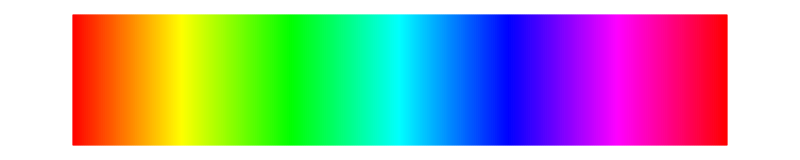

```mathematica
specLine
```

The simplest filters, point filters,  use a local neighborhood of size one (i.e., just the pixel value itself), and are limited in what they can accomplish. Once the neighborhood is enlarged to contain more points, the possibilities expand rapidly. For example, a neighborhood-three filter (as shown below) is defined by 9 numbers centered on w(0,0) and labeled w(x,y), for x=-1,0,1 and y=-1,0,1. The filtering process at a point (x,y) consists of combining the nine w( ) values with the nine and f( ) values to give a single number g(x,y) that is the value the output image assumes at the point (x,y). The filter then moves on to the next point, repeating the procedure for every point in the image. If the 18 numbers are combined in a very specific way, the filter is linear. If they are combined differently, the filter is nonlinear.

```mathematica
Labeled[GraphicsRow[{-Graphics-},ImageSize->420] ,"Nonlinear filters combine a mask w( ) with an image f( ) to create an output image",LabelStyle->captionStyle](* 2dimNonlinearFiltering.ai *)
```

-Graphics-Nonlinear filters combine a mask w( ) with an image f( ) to create an output image

The output g(x,y) can be calculated in many possible ways. For instance, all the corresponding pairs w(i,j) and f(x+i,y+j) could be multiplied, and then g(x,y) could be the maximum of the products. Or all the pairs w(i,j) and f(x+i,y+j) could be added, and g(x,y) could be the minimum of all the sums. Or the f(x+i,y+j)’s could all be averaged, and then g(x,y) could be 1 if f(0,0) is greater than the average and 0 if f(0,0) is less than the average. Or... or... there are a lot of possible ways to combine things!

```mathematica
specLine
```

-Graphics-

At the simplest level, there are a large number of built-in nonlinear filters and they are quite easy to apply. Here are a few:

```mathematica
labelNonlinearFilters="Mathematica contains a large number of built-in nonlinear filters";
infoNonlinearFilters="Try out each of the filters on a couple of different images to get a feel for them.\n\nFor example, the Commonest, Max and Min filters tend to give blocky results and to homogenize the overall color pallette.\n\nMin tends to darken the image while Max tends to lighten it.\n\nThe StandardDeviationFilter tends to be a colorful edge detection method (for small neighborhoods).";
Manipulate[ImageAdjust[filterType[allImagesColor[[i]],neighborhood]],
{{i,vermeerMilk,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu},{{filterType,CommonestFilter,"filter"},{MedianFilter,MinFilter,MaxFilter, CommonestFilter,StandardDeviationFilter}},
Row[{Control[{{neighborhood,10,"neighborhood"},1,20,1}],Spacer[20],info[infoNonlinearFilters]}],
FrameLabel->Style[labelNonlinearFilters,Medium],TrackedSymbols->{i,filterType,neighborhood},SynchronousUpdating->False,SaveDefinitions->saveDef]
```

The MinFilter[ ] (selected in the chooser box) looks in each neighborhood and finds the f(x-i,y-j) that is the smallest, and then lets g(x,y) be that smallest value, applying this to each of the three RGB color channels separately. Since smaller numbers are darker, the min filter tends to darken the image. Analogously, the MaxFilter[ ] lets the output g(x,y) be the largest of the f(x-i,y-j) in the neighborhood, lightening the image. The MedianFilter[ ] finds the middle value in the neighborhood, and the CommonestFilter[ ] looks through the neighborhood for the value that occurs most often. This tends to look blocky and to homogenize the color palette. The StandardDeviationFilter[ ] calculates the square root of the variance of the f( )’s in the neighborhood. So the areas with the largest deviations will be accentuated and areas of small deviation will be near zero.

```mathematica
specLine
```

-Graphics-

Of course, nonlinear filters can be used in combination. Here is the point-by-point product of any two of the nonlinear filters (when choosing to combine via ImageMultiply) or the difference between any two of the nonlinear filters (when combining via ImageSubtract). The longer you look, the more different effects you can find!

```mathematica
labelFilterDiff="This demonstration combines two nonlinear filters for a variety of effects";
infoFilterDiff="As with linear filters, nonlinear filters can be combined. Two methods are explored here, combining by subtracting and combining by multiplying.\n\nUnlike linear filters, the order matters when applying nonlinearities. Find an example where filter1 applied to filter2 of an image is not the same as filter2 applied to filter1 of the image.\n\nThe brightness is needed whenever the range of the pixel values becomes too compressed (the figure is mostly black) or too stretched (mostly white). Adjust to taste.";Manipulate[If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];ImageMultiply[combine[filterType1[img,neighborhood1],filterType2[img,neighborhood2]],bright],Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[5],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[5],Control[{{combine,ImageSubtract,"combining mode"},{ImageMultiply,ImageSubtract}}]}],{{filterType1,MedianFilter,"filter 1"},{MedianFilter,MinFilter,MaxFilter,CommonestFilter,StandardDeviationFilter}},{{neighborhood1,13,"neighborhood 1"},1,15,1},{{filterType2,MaxFilter,"filter 2"},{MedianFilter,MinFilter,MaxFilter,CommonestFilter,StandardDeviationFilter}},{{neighborhood2,2,"neighborhood 2"},1,15,1},Row[{Control[{{bright,15,"brightness"},0.1,20}],Spacer[10],info[infoFilterDiff]}],FrameLabel->Style[labelFilterDiff,Medium],TrackedSymbols->{i,filterType1,neighborhood1,filterType2,neighborhood2,bright,combine,invert},SynchronousUpdating->False,SaveDefinitions->saveDef]
```

HW: All of the filters in the above demonstration use a box-shaped neighborhood (the default). Implement a similar interactive demonstration that allows choice of a variety of neighborhoods with different shapes such as in this example.

```mathematica
specLine
```

-Graphics-

Here is the same thing operating on colored images.

```mathematica
labelFilterDiffColor="This demonstration combines two nonlinear filters operating on colored images for a variety of effects";
infoFilterDiffColor="As with linear filters, nonlinear filters can be combined. Two methods are explored here, combining by subtracting and combining by multiplying.\n\nUnlike linear filters, the order matters when applying nonlinearities. Find an example where filter1 applied to filter2 of an image is not the same as filter2 applied to filter1 of the image.\n\nThe brightness is needed whenever the range of the pixel values becomes too compressed (the figure is mostly black) or too stretched (mostly white). Adjust to taste.";;Manipulate[ImageMultiply[combine[filterType1[img=allImagesColor[[i]],neighborhood1],filterType2[img,neighborhood2]],bright],Row[{Control[{{i,vanTreeRoots,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[10],Control[{{combine,ImageMultiply,"combining mode"},{ImageMultiply,ImageSubtract}}],Spacer[10],info[infoFilterDiffColor]}],{{filterType1,MedianFilter,"filter 1"},{MedianFilter,MinFilter,MaxFilter,CommonestFilter,StandardDeviationFilter}},{{neighborhood1,10,"neighborhood 1"},1,15,1},{{filterType2,StandardDeviationFilter,"filter 2"},{MedianFilter,MinFilter,MaxFilter,CommonestFilter,StandardDeviationFilter}},{{neighborhood2,1,"neighborhood 2"},1,15,1},{{bright,10,"brightness"},0.1,20},FrameLabel->Style[labelFilterDiffColor,Medium],TrackedSymbols->{i,filterType1,neighborhood1,filterType2,neighborhood2,bright,combine},SynchronousUpdating->False,SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Here is a list of all the Mathematica filters, many of which are nonlinear:

```mathematica
?*Filter
```

HW: Can you tell which of the above filters are actually linear?

Here is an implementation of some of these.

```mathematica
labelNonlinearFiltersXRay="An assortment of nonlinear filters applied to x-ray images";
infoNonlinearFiltersXRay="To familiarize yourself with some of these filters, here are a few things to try:\n\nPick a filter (and neighborhood) to emphasize the cracks in L17.\n\nPick a filter (and neighborhood size) locate the outline of the staple in L11Diag24.\n\nFor some filters, operating on the positive gives the same results as operating on the negative.";
Manipulate[If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];ImageAdjust[filterType[img,neighborhood]],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],Control[{{filterType,RangeFilter,"filter"},{CornerFilter,CurvatureFlowFilter,EntropyFilter,KuwaharaFilter,PeronaMalikFilter,RangeFilter,TotalVariationFilter,WienerFilter}}]}],
Row[{Control[{{neighborhood,2,"neighborhood"},1,20,1}],Spacer[20],info[infoNonlinearFiltersXRay]}],
FrameLabel->Style[labelNonlinearFiltersXRay,Medium],SynchronousUpdating->False,TrackedSymbols->{i,filterType,neighborhood,invert},SaveDefinitions->saveDef]
```

HW: Another built-in nonlinear filter is the MeanShiftFilter[ ] which takes two parameters: a neighborhood size and a range value (between zero and one). Apply the MeanShiftFilter[ ] to the thread x-ray images and describe the effects you see.

```mathematica
specLine
```

-Graphics-

Of course, it’s also possible to roll your own filters. This is a fairly large topic, and is discussed in length in Inside Nonlinear Filters. As a teaser of what is possible, here is an adaptive thresholding filter. In normal thresholding, a value is chosen and all pixel values above the threshold are turned to white and all below are turned to black. An adaptive threshold changes based on the context; in this case, it finds the mean value in a neighborhood, and if the pixel is greater than threshold*mean, then it becomes white, otherwise it is set to black. This gives a much greater flexibility in the binarization process then when using a simple threshold. The central function is ImageFilter[ ], which allows the user to define any kind of local processing desired:  in this case, the function adaptThresh[ ] was designed specially for this purpose.

```mathematica
labelAdaptThresh="Adaptive thresholding chooses the threshold based on the local character of the image";
infoAdaptThresh="Adaptive thresholding is a more sophisticated way to binarize based on the data in the image (and not just on a single threshold).\n\nIn this implementation, you can control two things: the size of the neighborhood that is considered at any one time, and a threshold that will be used (based on the pixel values in the neighborhood).\n\nThe operation of the algorithm is defined by the function adaptThresh[ ]. Take the mean of the pixels in the neighborhood, if the center pixel is greater than the threshold times the mean, set it to one (otherwise set it to zero).\n\nThe default parameters show how this can nicely separate the thread peaks from the valleys.";
adaptThresh[x_]:=Module[{},meanX=Mean[Flatten[x]];
center=Floor[Sqrt[Length[Flatten[x]]]/2];
thisPix=x[[center,center]];
Boole[thisPix>threshRat meanX]];
Manipulate[threshRat=tau;If[invert=="negative",img=allImagesXray[[i]],img=ColorNegate[allImagesXray[[i]]]];
ImageFilter[adaptThresh,img,n],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{invert,"negative",""},{"negative","positive"}}],Spacer[20],info[infoAdaptThresh]}],
{{n,9,"neighborhood"},1,30,1},
{{tau,1,"threshold ratio"},0.95,1.1},
FrameLabel->Style[labelAdaptThresh,Medium],SynchronousUpdating->False,TrackedSymbols->{i,n,tau,invert},SaveDefinitions->saveDef]
```